# Import functions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["funcs_oscillation_range.m"]
```

# Plot stoch sims

```mathematica
ip3s={
"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000",
"ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"
};
```

```mathematica
volExp=12;
volStr="10^-12";

noIP3R=1000;
fnameIdxStart=0;
fnameIdxEnd=99;
dataDir=NotebookDirectory[]<>"../ml_training_data/data_gillespie/";

dataCa2i=importCa2i[volExp,noIP3R,fnameIdxStart,fnameIdxEnd,dataDir,ip3s];
```

```mathematica
avogadro=6.02214076*^23;
plts=Association[];
Monitor[
Do[
ip3=ip3s[[i]];

dataPlt=dataCa2i[ip3];
dataPlt[[;;,;;,2]]*=10^6/(10^(-1*volExp)*avogadro);

plt=Show[
ListLinePlot[dataPlt,PlotRange->{0,1.0},PlotStyle->LightGray],
ListLinePlot[Mean[dataPlt],PlotRange->All,PlotStyle->Red],
PlotLabel->"[IP3]: " <>ToString[pStrToNo[ip3]]<>" μM",
ImageSize->300,
FrameLabel->{"time (s)",None}
];

plts[ip3]=plt;
,{i,Length[ip3s]}];
,ProgressIndicator[i,{1,Length[ip3s]}]]
```

```mathematica
label=Style["Vol: "<>volStr<>" L & # IP3R: "<>ToString[noIP3R],FontSize->36];
leg=LineLegend[{LightGray,Red},{"[Ca^(2+)] in cytosol","Mean [Ca^(2+)]"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
pltTog=Grid[{{label},{
Grid[
ArrayReshape[
Values[plts][[;;;;2]],
{5,2}
]]
,
leg
}}];
```

# Range of oscillations

## Setup

```mathematica
ip3s={
"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000",
"ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"
};
```

## True diagram

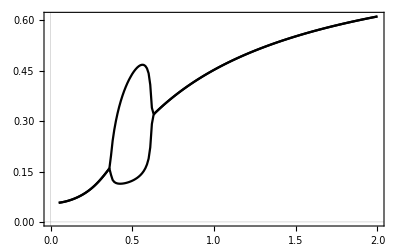

```mathematica
SetDirectory[NotebookDirectory[]];
caMinTrue=Import["oscillation_range_data/diff_eq_min.txt","Table"];
caMaxTrue=Import["oscillation_range_data/diff_eq_max.txt","Table"];

pltTrue=ListLinePlot[{caMinTrue,caMaxTrue},PlotStyle->Black]
```

## Vol exp = 12

## Run 12

```mathematica
fnameIdxStart=0;
fnameIdxEnd=99;

volExp=12;
noIP3RsAndDirs={
{100,NotebookDirectory[]<>"../ml_training_data/data_gillespie/"},
{1000,NotebookDirectory[]<>"../ml_training_data/data_gillespie/"}
};
noIP3Rs=noIP3RsAndDirs[[;;,1]];

{ca2iMin,ca2iMax}=makeCa2iBifs[volExp,noIP3RsAndDirs,ip3s,fnameIdxStart,fnameIdxEnd];
```

## Export data 12

```mathematica
exportDataBif[volExp,ca2iMin,ca2iMax]
```

## Import data 12

```mathematica
volExp=12;
noIP3Rs={100,1000};
{ca2iMin,ca2iMax}=importDataBif[volExp,noIP3Rs];
```

## Plot 12

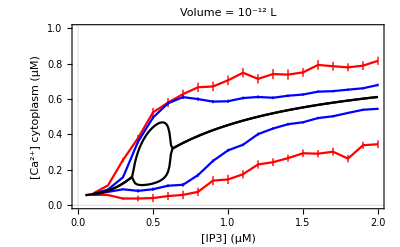

```mathematica
plts={};
colsMin={Red,Blue,Darker[Green]};
colsMax={Red,Blue,Darker[Green]};
Do[
noIP3R=noIP3Rs[[i]];

plt=ListLinePlot[
{ca2iMin[noIP3R],ca2iMax[noIP3R]},
PlotRange->{0,1.0},
PlotStyle->{{colsMin[[i]]},{colsMax[[i]]}},
PlotLabel->"Volume = 10^-12 L",
FrameLabel->{"[IP3] (μM)","[Ca^(2+)] cytoplasm (μM)"}
];
AppendTo[plts,plt];
,{i,1,Length[noIP3Rs]}];

plt12=Show[plts,pltTrue]
```

## Export plot

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/diagram_12.pdf",plt12];
```

## Vol exp = 14

## Run 14

```mathematica
fnameIdxStart=0;
fnameIdxEnd=99;

volExp=14;
(*
noIP3RsAndDirs={
{100,NotebookDirectory[]<>"../ml_training_data/data_gillespie/"},
{1000,NotebookDirectory[]<>"../ml_training_data/data_tau_leaping/"},
{5000,NotebookDirectory[]<>"../ml_training_data/data_tau_leaping/"}
};
*)
noIP3RsAndDirs={
{500,NotebookDirectory[]<>"../ml_training_data/data_gillespie/"},
{600,NotebookDirectory[]<>"../ml_training_data/data_gillespie/"},
{700,NotebookDirectory[]<>"../ml_training_data/data_gillespie/"},
{800,NotebookDirectory[]<>"../ml_training_data/data_gillespie/"},
{900,NotebookDirectory[]<>"../ml_training_data/data_gillespie/"}
};
noIP3Rs=noIP3RsAndDirs[[;;,1]];

{ca2iMin,ca2iMax}=makeCa2iBifs[volExp,noIP3RsAndDirs,ip3s,fnameIdxStart,fnameIdxEnd];
```

## Export data 14

```mathematica
exportDataBif[volExp,ca2iMin,ca2iMax]
```

## Import data 14

```mathematica
volExp=14;
noIP3Rs={100,1000,5000};
{ca2iMin,ca2iMax}=importDataBif[volExp,noIP3Rs];
```

## Plot 14

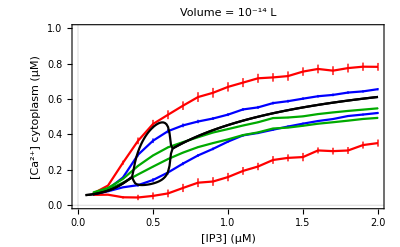

```mathematica
plts={};
colsMin={Red,Blue,Darker[Green]};
colsMax={Red,Blue,Darker[Green]};
Do[
noIP3R=noIP3Rs[[i]];

plt=ListLinePlot[
{ca2iMin[noIP3R],ca2iMax[noIP3R]},
PlotRange->{0,1.0},
PlotStyle->{{colsMin[[i]]},{colsMax[[i]]}},
PlotLabel->"Volume = 10^-14 L",
FrameLabel->{"[IP3] (μM)","[Ca^(2+)] cytoplasm (μM)"}
];
AppendTo[plts,plt];
,{i,1,Length[noIP3Rs]}];

plt14=Show[plts,pltTrue]
```

## Export plot

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/diagram_14.pdf",plt14];
```

## Together

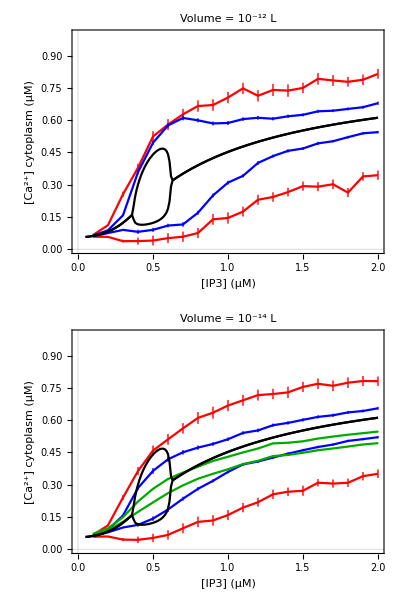
-Graphics- |

```mathematica
leg=LineLegend[{Red,Blue,Darker[Green],Black},{"# IP3R = 100","# IP3R = 1000", "# IP3R = 5000","De Young & Keizer"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];

pltBif=Grid[{{Grid[{
{plt12},
{plt14}}],leg}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/range_of_oscillations.pdf",pltBif];
Export["figures/leg.pdf",leg];
```

```mathematica
leg1=LineLegend[{Red,Blue},{"# IP3R = 100","# IP3R = 1000"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
leg2=LineLegend[{Darker[Green],Black},{"# IP3R = 5000","De Young & Keizer"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40];
SetDirectory[NotebookDirectory[]];
Export["figures/leg1.pdf",leg1]
Export["figures/leg2.pdf",leg2]
```

figures/leg1.pdf

figures/leg2.pdf